```mathematica
Needs["PlotLegends`"]
Mh=125.7 (* masa del higgs en GeV *);
alfa=1.64; (* 95% CL *)
SigHZ=6.1*10^-5; (* seccion eficaz e^+e^- --> HZ en fb *)
SigHnunu=8.5*10^-5; (* seccion eficaz e^+e^- --> Hnunu en fb *)
BrSMtt=6.32*10^-2; (* Branching ratio del higgs a τ^+τ^- fb *)
BrSMbb=5.77*10^-2; (* Branching ratio del higgs a b bbar *)
GHT=4.07*10^-3; (* ancho decaimiento total Higgs en GeV *)
dFtt[L_]:=-9.68*Log[(L/Mh)^2]/(L^2*GHT); (* delta Br 4 fermiones H --> TT *)
dFbb[L_]:=-159*Log[(L/Mh)^2]/(L^2*GHT); (* delta Br 4 fermiones H --> bb *)
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Set::write: Tag ListLinePlot in SyntaxInformation[ListLinePlot] is Protected.

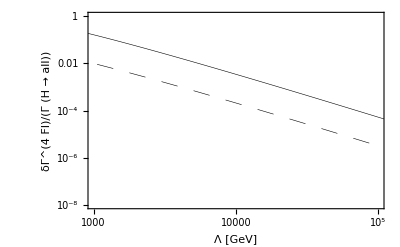

```mathematica
LogLogPlot[{(-1)*dFbb[L],(-1)*dFtt[L]},{L,10,10^6},PlotRange->{{1000,10^5},{10^-8,1}},Frame-> True,FrameLabel->{"Λ [GeV]","δΓ^(4  FI)/(Γ (H →  all))"},LabelStyle ->Directive[Black,FontFamily->"Helvetica"],PlotStyle->{Directive[Black,Thickness[0.001]],Directive[Thickness[0.001],Black,Dashing[{.03}]]},PlotLegend->{Style["H → b b̄",Black,8] 
       , Style["H → τ^+τ^-",Black,8]},LegendPosition->{0.3,0.3},LegendTextSpace->2.5,LegendLabel->Style["",0],LegendLabelSpace->.1,LegendOrientation->Vertical,LegendBackground->White,LegendShadow->{.02,-.02},Background->White,LegendSize->{0.4,0.2}]
```

```mathematica
Export["/home/felipe/Desktop/Br4f.pdf",%]
```

/home/felipe/Desktop/Br4f.pdf

```mathematica
Listbb:=Table[{i,(-1)*dFbb[i]},{i,1000,10^5,100}]
Listtt:=Table[{i,(-1)*dFtt[i]},{i,1000,10^5,100}]
```

```mathematica
Export["/home/felipe/Dropbox/4_Fermiones/dFbb.dat",Listbb]
Export["/home/felipe/Dropbox/4_Fermiones/dFtt.dat",Listtt]
```

/home/felipe/Dropbox/4_Fermiones/dFbb.dat

/home/felipe/Dropbox/4_Fermiones/dFtt.dat

-(747.74 Log[0.0000632892 L^2])/L^2

-(106.672 Log[0.0000632892 L^2])/L^2

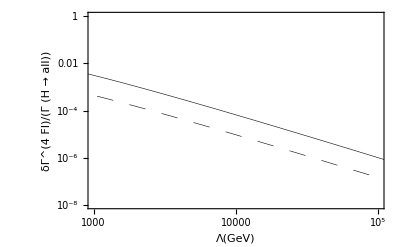

```mathematica
(*SOLO PARTE AXIAL*)


Mtau=1.776 ;      (*Pag 31 PDG2014*)
Mb=4.18 ;
MW=80.385 ;  (*Pag 27 PDG2014*)
v=246 ;       (**)
g=2MW/v;

(*solo contribucion axial*)
SAx[Mf_,L_]:=((g^2*Mh*Mf)/(16*π*MW^2))*(1-4*Mf^2/Mh^2)^(3/2)*(-3/(32*L^2))*(Mh^2-2 Mf^2)*Log[L^2/Mh^2];
dFSAxbb=SAx[Mb,L]*3/GHT
dFSaxtt=SAx[Mtau,L]/GHT

LogLogPlot[{(-1)*dFSAxbb, (-1)*dFSaxtt},{L,10^2,10^6},PlotRange->{{1000,10^5},{10^-8,1}},Frame-> True,FrameLabel->{"Λ"[GeV],"δΓ^(4  FI)/(Γ (H →  all))"},LabelStyle ->Directive[Black,FontFamily->"Helvetica"],PlotStyle->{Directive[Black,Thickness[0.001]],Directive[Thickness[0.001],Black,Dashing[{.03}]]},PlotLegend->{Style["H → b b̄",Black,8] 
       , Style["H → τ^+τ^-",Black,8]},LegendPosition->{0.3,0.3},LegendTextSpace->2.5,LegendLabel->Style["",0],LegendLabelSpace->.1,LegendOrientation->Vertical,LegendBackground->White,LegendShadow->{.02,-.02},Background->White,LegendSize->{0.4,0.2}]
```

```mathematica
FSAxbb[L_]:=-(747.74*Log[(L/Mh)^2])/L^2
FSAxtt[L_]:=-(106.672*Log[(L/Mh)^2])/L^2
```

```mathematica
ListbbNew:=Table[{i,(-1)*FSAxbb[i]},{i,1000,10^5,100}]
ListttNew:=Table[{i,(-1)*FSAxtt[i]},{i,1000,10^5,100}]
```

```mathematica
Export["/home/felipe/Desktop/dFbb_ax.dat",ListbbNew]
Export["/home/felipe/Desktop/dFtt_ax.dat",ListttNew]
```

/home/felipe/Desktop/dFbb_ax.dat

/home/felipe/Desktop/dFtt_ax.dat

```mathematica
Export["/home/felipe/Desktop/Br4f_solo_axial.pdf",%]
```

/home/felipe/Desktop/Br4f_solo_axial.pdf

```mathematica
dFSAxbb=SAx[Mb]*3
dFSaxtt=SAx[Mtau]
```

-(3.0433 Log[0.0000632892 L^2])/L^2

-(0.434156 Log[0.0000632892 L^2])/L^2

Comparacion

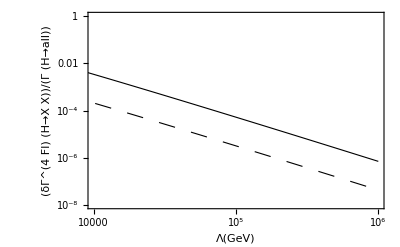

```mathematica
LogLogPlot[{(-1)*dFbb[L],(-1)*dFtt[L],(-1)*dFSAxbb, (-1)*dFSaxtt},{L,10^2,10^6},PlotRange->{{10^4,10^6},{10^-8,1}},Frame-> True,FrameLabel->{"Λ"[GeV],(δΓ^(4FI)(H->"X X"))/(Γ(H-> all))},LabelStyle ->Directive[Black,FontFamily->"Helvetica"],PlotStyle->{Directive[Black,Thickness[0.002]],Directive[Thickness[0.002],Black,Dashing[{.03}]],Directive[Red,Thickness[0.002]],Directive[Thickness[0.002],Red,Dashing[{.03}]]},PlotLegend->{Style["H → b b̄",Black,8],Style["H → b b̄",Black,8],Style["Axial:  H → b b̄",Red,8] 
       , Style["Axial:  H → τ^+τ^-",Red,8]},LegendPosition->{0.5,0.15},LegendTextSpace->3,LegendLabel->Style["",0],LegendLabelSpace->.1,LegendOrientation->Vertical,LegendBackground->White,LegendShadow->{.02,-.02},Background->White,LegendSize->{0.8,0.4}]
```

```mathematica
Export["/home/felipe/Desktop/Br4f_comparacion.pdf",%]
```

/home/felipe/Desktop/Br4f_comparacion.pdf

## nuevo

```mathematica
SAnew[MH_,Mf_,L_]:=((g^2*MH*Mf)/(16*π*MW^2))*(1-4*Mf^2/MH^2)^(3/2)*(-3/(32*L^2))*(MH^2-2 Mf^2)*Log[L^2/MH^2]
```

```mathematica
FSAbbnew3T[MH_]:=(-1)*SAnew[MH,Mb,3000]*3
FSAbbnew15T[MH_]:=(-1)*SAnew[MH,Mb,15000]*3
FSAbbnew30T[MH_]:=(-1)*SAnew[MH,Mb,30000]*3
FSAttnew3T[MH_]:=(-1)*SAnew[MH,Mtau,3000]
FSAttnew15T[MH_]:=(-1)*SAnew[MH,Mtau,15000]
FSAttnew30T[MH_]:=(-1)*SAnew[MH,Mtau,30000]
```

```mathematica
ListFSAbbN3T:=Table[{i,FSAbbnew3T[i]},{i,100,3000,10}]
ListFSAbbN15T:=Table[{i,FSAbbnew15T[i]},{i,100,15000,10}]
ListFSAbbN30T:=Table[{i,FSAbbnew30T[i]},{i,100,30000,10}]
ListFSAttN3T:=Table[{i,FSAttnew3T[i]},{i,100,3000,10}]
ListFSAttN15T:=Table[{i,FSAttnew15T[i]},{i,100,15000,10}]
ListFSAttN30T:=Table[{i,FSAttnew30T[i]},{i,100,30000,10}]
```

```mathematica
Export["/home/felipe/Desktop/dFSAbb_3T.dat",ListFSAbbN3T]
Export["/home/felipe/Desktop/dFSAbb_15T.dat",ListFSAbbN15T]
Export["/home/felipe/Desktop/dFSAbb_30T.dat",ListFSAbbN30T]
Export["/home/felipe/Desktop/dFSAtt_3T.dat",ListFSAttN3T]
Export["/home/felipe/Desktop/dFSAtt_15T.dat",ListFSAttN15T]
Export["/home/felipe/Desktop/dFSAtt_30T.dat",ListFSAttN30T]
```

/home/felipe/Desktop/dFSAbb_3T.dat

/home/felipe/Desktop/dFSAbb_15T.dat

/home/felipe/Desktop/dFSAbb_30T.dat

/home/felipe/Desktop/dFSAtt_3T.dat

/home/felipe/Desktop/dFSAtt_15T.dat

/home/felipe/Desktop/dFSAtt_30T.dat

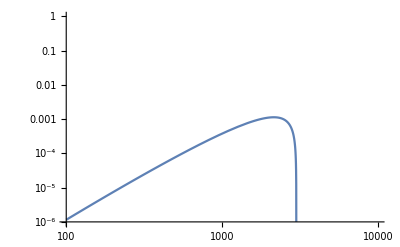

```mathematica
LogLogPlot[{FSAbbnew3T[MH]},{MH,10^2,10^5},PlotRange->{{10^2,10^4},{10^-6,1}}]
```